## AMO Physics Notebook 1 Author: Huan Q. Bui Massachusetts Institute of Technology First updated: Jan 30, 2023 Last updated: Feb 01, 2023

### List of Constants (SI units)

General Physics Constants

```mathematica
cSOL=2.99792458*10^8; (*m/s*)
```

```mathematica
hbar=1.05457182*10^(-34); (*J s*)
```

```mathematica
ϵ0=8.8541878128*10^(-12);(*F/m*)
```

```mathematica
e=1.60217663*10^(-19);(*Coulombs*)
```

```mathematica
mE=9.1093837*10^(-31);(*kg*)
```

```mathematica
μB=e*hbar/(2*mE);(*Bohr magneton in Joules per Tesla*)
```

```mathematica
μBFreq = hbar*2*Pi*1.399624604; (*MHz/G*)
```

```mathematica
γE=e/mE; (*electron gyromagnetic ratio*)
```

Can also write γ_E=-g_sμ_B/ℏ, where g_s=2 from Dirac theory.

```mathematica
μE=γE*S; (*Here S = ℏ/2, the electron's spin angular momentum*)
```

```mathematica
α=e^2/(4*Pi*ϵ0*hbar*cSOL); (*Fine-structure constant ~ 1/137*)
```

g-factors:

```mathematica
gL=0.99999587;(*electron L=1 orbital g-factor*)
```

```mathematica
gS=2.0023193043737; (*electron spin g-factor*)
```

```mathematica
gF[F_,II_,J_,gJ_,gI_]:=gJ*( (F*(F+1)-II*(II+1) +J*(J+1)) /(2*F*(F+1)))+gI*(  (F*(F+1)+II*(II+1)-J*(J+1)) /(2*F*(F+1)));
```

Lithium-6 Constants

```mathematica
mLi6=9.9883414*10^(-27); (*kg*)
```

```mathematica
λLi6D2=670.977338*10^(-9); (*m*)
```

```mathematica
ωLi6D2=2*Pi*446.799677*10^(12);(*Hz*)
```

```mathematica
ΓLi6D2=2*Pi*5.8724*10^6; (*MHz -- angular frequency *)
```

```mathematica
vRecoilLi6D2=0.09886776 ;(*m/s*)
```

```mathematica
TRecoilLi6D2=3.53581152*10^(-6); (*Kelvin*)
```

Lithium-6 g-factors:

```mathematica
gILi6=-0.0004476540; (*total nuclear g-factor*)
```

```mathematica
gJLi6S12=2.0023010; (*gJ for 2 Subscript[S, 1/2]*)
```

```mathematica
gJLi6P12=0.6668; (*gJ for 2 Subscript[P, 1/2]*)
```

```mathematica
gJLi6P32=1.335; (*gJ for 2 Subscript[P, 3/2]*)
```

Sodium-23 Constants

```mathematica
mNa23=0.381754035*10^(-25); (*kg*)
```

```mathematica
λNa23D2=589.1583264*10^(-9);(*m*)
```

```mathematica
ωNa23D2=2*Pi*508.8487162*10^(12);(*Hz*)
```

```mathematica
ΓNa23D2=2*Pi*9.7946*10^6;(*Hz*)
```

```mathematica
vRecoilNa23D2=0.029461; (*m/s*)
```

```mathematica
TRecoilNa23D2=2.3998*10^(-6); (*Kelvin*)
```

Sodium-23 g-factors:

```mathematica
gINa23=0;
```

```mathematica
gJNa23S12=0;
```

```mathematica
gJNa23P12=0;
```

```mathematica
gJNa23P32=0;
```

### Two-Level System: Resonance

Classical Spin in Time-Varying Magnetic Field

Rapid Adiabatic Passage: Landau-Zener Crossing, Classical Treatment

The Hamiltonian of a Quantized Spin-1/2 in a Rotating Magnetic Field

Consider a spin-1/2 in a magnetic field which points along the z-axis. Then the unperturbed Hamiltonian takes the form

H_0 = - μ.B = -μ_z B_z = -γS_z B_z = -S_z ω_0 = (-ℏω_0/2) σ_z

where we have put ω_0= -γB_z to be the bare Larmor frequency.

```mathematica
H0Spin12=-(ℏ*ω0/2)*PauliMatrix[3];
```

```mathematica
H0Spin12//MatrixForm
```

(-(ω0 ℏ)/2 | 0
0 | (ω0 ℏ)/2)

The perturbed Hamiltonian takes into account the presence of a rotating magnetic field in the xy-plane in the clockwise direction. 
The Hamiltonian now takes the form:

H_1 = - μ.B_R = -γ S.B_R = (-γ|B_R|)ℏ/2 * (σ_x Cos[ωt] - σ_y Sin[ωt]) = (-ℏω_R/2)*(σ_x Cos[ωt] - σ_y Sin[ωt])

where we have put ω_R = γB_R and ω is the frequency of the rotating magnetic field. “R” here stands for “rotating” but as we will see “R” will also stand for “Rabi.”

```mathematica
H1Spin12 = -(ℏ*ωR/2)*(Cos[ω *t]*PauliMatrix[1] - Sin[ω*t]*PauliMatrix[2]);
```

```mathematica
H1Spin12//FullSimplify//MatrixForm
```

(0 | -1/2 ⅇ^(ⅈ t ω) ωR ℏ
-1/2 ⅇ^(-ⅈ t ω) ωR ℏ | 0)

With H_0 and H_1we have the full Hamiltonian:

```mathematica
HSpin12 = H0Spin12 + H1Spin12//FullSimplify;
```

```mathematica
HSpin12//MatrixForm
```

(-(ω0 ℏ)/2 | -1/2 ⅇ^(ⅈ t ω) ωR ℏ
-1/2 ⅇ^(-ⅈ t ω) ωR ℏ | (ω0 ℏ)/2)

Solution via the rotating frame

The problem simplifies a big deal when we go to the frame which rotates with the rotating magnetic field at angular frequency -ω (since we assume that the magnetic field is rotating clockwise). The operator which takes us to this rotating frame is:

T = Exp[ -i * σ_z/2 * θ] 

where θ is the angle of rotation which we set to θ = -ω t. With these, the transformation operator T is:

```mathematica
T= MatrixExp[-I*PauliMatrix[3]/2*(-ω*t)];
```

```mathematica
T//MatrixForm
```

(ⅇ^((ⅈ t ω)/2) | 0
0 | ⅇ^(-1/2 ⅈ t ω))

How does the Hamiltonian transform by going to the rotating frame? It is not simply T*HT as one might expect. To get the new Hamiltonian, one has to write down the Schrodinger equation for the original Hamiltonian, then replace the original kets by T applied to kets in the rotating frame:

ψ(t) = T(t) ψ_rot(t)

One then rearrange this new equation into a new Schrodinger equation for ψ_rot(t) and look at the form of the new Hamiltonian, which one will call H_rot which is given by:

```mathematica
HRot = FullSimplify[ConjugateTranspose[T].HSpin12.T - I*ℏ*ConjugateTranspose[T].D[T,t],{t>0,ω>0}];
```

```mathematica
HRot//MatrixForm
```

(1/2 (ω-ω0) ℏ | -(ωR ℏ)/2
-(ωR ℏ)/2 | 1/2 (-ω+ω0) ℏ)

Introducing the detuning parameter δ  = ω - ω0, we have

```mathematica
HRotδ=FullSimplify[HRot]/.{ω->δ+ω0};
```

```mathematica
HRotδ//MatrixForm
```

((δ ℏ)/2 | -(ωR ℏ)/2
-(ωR ℏ)/2 | -(δ ℏ)/2)

The result above is the Hamiltonian for the system in the frame co-rotating with the magnetic field.

The eigensystem associated with this Hamiltonian is:

```mathematica
Eigensystem[HRotδ]
```

{{-1/2 √(δ^2+ωR^2) ℏ,1/2 √(δ^2+ωR^2) ℏ},{{-(δ-√(δ^2+ωR^2))/ωR,1},{-(δ+√(δ^2+ωR^2))/ωR,1}}}

The energies (eigenvalues) are

```mathematica
Eigenvalues[HRotδ]
```

{-1/2 √(δ^2+ωR^2) ℏ,1/2 √(δ^2+ωR^2) ℏ}

The energies are +/- ℏΩ/2 where Ω is the generalized Rabi frequency. The unnormalized eigenvectors are:

```mathematica
EigenvectorsRotUnnormalized=(ωR/ΩR)*Eigenvectors[HRotδ]/.{√(δ^2+ωR^2)->ΩR}//Expand
```

{{1-δ/ΩR,ωR/ΩR},{-1-δ/ΩR,ωR/ΩR}}

Define the angle ϕ via the following rules:

```mathematica
FreqsToϕ={δ/ΩR->Cos[ϕ],ωR/ΩR->-Sin[ϕ]};
```

Then the eigenvectors become

```mathematica
EigenvectorsRotUnnormalizedϕ=EigenvectorsRotUnnormalized/.FreqsToϕ
```

{{1-Cos[ϕ],-Sin[ϕ]},{-1-Cos[ϕ],-Sin[ϕ]}}

```mathematica
GroundStateRot=-FullSimplify[EigenvectorsRotUnnormalizedϕ[[2]]/Sqrt[EigenvectorsRotUnnormalizedϕ[[2]].EigenvectorsRotUnnormalizedϕ[[2]]]/.{Cos[ϕ]->2*Cos[ϕ/2]^2-1,Sin[ϕ]->2*Sin[ϕ/2]*Cos[ϕ/2]},Cos[ϕ/2]>0]; (*minus sign picked to get nice phase*)
```

```mathematica
GroundStateRot//MatrixForm
```

(Cos[ϕ/2]
Sin[ϕ/2])

```mathematica
ExcitedStateRot=FullSimplify[EigenvectorsRotUnnormalizedϕ[[1]]/Sqrt[EigenvectorsRotUnnormalizedϕ[[1]].EigenvectorsRotUnnormalizedϕ[[1]]]/.{Cos[ϕ]->2*Cos[ϕ/2]^2-1,Sin[ϕ]->2*Sin[ϕ/2]*Cos[ϕ/2]},Sin[ϕ/2]<0];
```

```mathematica
ExcitedStateRot//MatrixForm
```

(-Sin[ϕ/2]
Cos[ϕ/2])

With these we can now write the solution in the rotating frame In terms of the basis states g = (1  0) and e = (0  1).

In order to obtain the solution to the original problem, we have to convert these back into the lab frame via the T operator defined above. Suppose that initially ψ is in the ground state g = (1  0) = cos(ϕ/2) gRot + sin(ϕ/2) eRot:

```mathematica
Cos[ϕ/2]*GroundStateRot-Sin[ϕ/2]*ExcitedStateRot//FullSimplify
```

{1,0}

The wavefunction in the rotating frame ψRot at t = 0 is also equal to g = (1  0). From here, we can apply the time-evolution operator in terms of the Hamiltonian in the rotating frame HRotδ in order to get the wavefunction at time t (the matrix exponentiation is easy when ψRot is written in the eigenbasis for HRotδ. Finally, to get the wavefunction in the lab frame, we apply the operator T to ψRot(t) to get ψ(t).

```mathematica
ψt = ExpToTrig[T.(Cos[ϕ/2]*Exp[-I*ΩR*t/2] *GroundStateRot   -   Sin[ϕ/2]*Exp[I*ΩR*t/2]*ExcitedStateRot)]//FullSimplify;
```

```mathematica
ψt//MatrixForm
```

(ⅇ^((ⅈ t ω)/2) (Cos[(t ΩR)/2]-ⅈ Cos[ϕ] Sin[(t ΩR)/2])
-ⅈ ⅇ^(-1/2 ⅈ t ω) Sin[ϕ] Sin[(t ΩR)/2])

From here, we can readily calculate the probability of observing the atom in the excited state e = (0  1):

```mathematica
P2Rabi = FullSimplify[FullSimplify[Abs[ψt.{0,1}]^2,{t>0,ω>0,Sin[(t ΩR)/2]>0}]/.{Sin[ϕ]->ωR/ΩR},{ωR>0,ΩR>0}]/.{ΩR->Sqrt[δ^2+ωR^2]};
```

```mathematica
P2Rabi
```

(ωR^2 Sin[1/2 t √(δ^2+ωR^2)]^2)/(δ^2+ωR^2)

As an example, we can see what P2 looks like as a function of detuning for different pulse lengths t:

```mathematica
Manipulate[Plot[(ωR^2 Sin[1/2 t √(δ^2+ωR^2)]^2)/(δ^2+ωR^2)/.{ωR->1},{δ,-3,3},PlotRange->{0,1}],{t,0,6*Pi}]
```

Rapid Adiabatic Passage: Landau-Zener Crossing, Quantum Treatment

The Hamiltonian

Consider the Hamiltonian for a spin-1/2 in the presence of a static magnetic field in the quantization axis and a rotating magnetic field in the xy-plane:

```mathematica
HSpin12//MatrixForm
```

(-(ω0 ℏ)/2 | -1/2 ⅇ^(ⅈ t ω) ωR ℏ
-1/2 ⅇ^(-ⅈ t ω) ωR ℏ | (ω0 ℏ)/2)

Let us define a similar but separate Hamiltonian for this section:

```mathematica
HLZ = (ℏ/2)*{{ω0,ωR*E^(-I*ϕ[t])},{ωR*E^(+I*ϕ[t]),-ω0}};
```

```mathematica
HLZ//MatrixForm
```

((ω0 ℏ)/2 | 1/2 ⅇ^(-ⅈ ϕ[t]) ωR ℏ
1/2 ⅇ^(ⅈ ϕ[t]) ωR ℏ | -(ω0 ℏ)/2)

Now suppose that we sweep the frequency, so that ωt becomes ϕ(t) which is generic. Going to rotating frame requires the operator T:

```mathematica
Tϕ= MatrixExp[-I*(PauliMatrix[3]/2)*ϕ[t]];
```

The Hamiltonian in the rotating frame is thus:

```mathematica
HLZRot = FullSimplify[ConjugateTranspose[Tϕ].HLZ.Tϕ - I*ℏ*ConjugateTranspose[Tϕ].D[Tϕ,t],{t>0,ϕ[t]>0}]/.{ω0->ϕ'[t]-δ[t]};
```

```mathematica
HLZRot//MatrixForm
```

(-1/2 ℏ δ[t] | (ωR ℏ)/2
(ωR ℏ)/2 | 1/2 ℏ δ[t])

where the detuning is now δ(t) = ϕ’(t) - ω0.

It turns out that this Hamiltonian is more difficult to deal with than the one we would get if we were to rotate with frequency ω0. The Hamiltonian in this frame is obtain from the rotating operator Tω0:

```mathematica
Tω0=MatrixExp[-I*(PauliMatrix[3]/2)*ω0*t];
```

```mathematica
HLZRotω0 = FullSimplify[ConjugateTranspose[Tω0].HLZ.Tω0 - I*ℏ*ConjugateTranspose[Tω0].D[Tω0,t],{t>0,ω0>0}];
```

```mathematica
HLZRotω0//MatrixForm
```

(0 | 1/2 ⅇ^(ⅈ (t ω0-ϕ[t])) ωR ℏ
1/2 ⅇ^(-ⅈ t ω0+ⅈ ϕ[t]) ωR ℏ | 0)

Weak Coupling Limit

Let ψ(t) = {a(t)    b(t)}. Then the Schrodinger’s equation for ψ(t) give two equations:

```mathematica
LZEqn1=a'[t]==-I*ωR/2 ⅇ^(ⅈ (t ω0-ϕ[t])) * b[t];
```

```mathematica
LZEqn2=b'[t]==-I*ωR/2 ⅇ^(-ⅈ t ω0+ⅈ ϕ[t]) * a[t];//FullSimplify
```

Suppose further that the sweep is linear, so ϕ’(t) = ω0+β t. This means

```mathematica
LZEqn1=LZEqn1/.{ϕ[t]->ω0*t+β*t^2/2}
```

a'[t]==-1/2 ⅈ ⅇ^(-1/2 ⅈ t^2 β) ωR b[t]

```mathematica
LZEqn2 =LZEqn2/.{ϕ[t]->ω0*t+β*t^2/2}//FullSimplify
```

b'[t]==-1/2 ⅈ ⅇ^(1/2 ⅈ t^2 β) ωR a[t]

Before solving this numerically here, we can consider the case of weak coupling where b ~ 1 at all times. In this case, we have from the “a” equation that the probability of seeing the atom in the ground state (1  0) is |a|^2. To find this, we first calculate a(t) from the a’(t) equation with the condition that b(t) = 1 for all t:

```mathematica
Integrate[-1/2 ⅈ ⅇ^(-1/2 ⅈ t^2 β) ωR,{t,-Infinity,Infinity}]
```

ConditionalExpression[-(ⅈ √(π/2) ωR)/(√(ⅈ β)), Im[β]<0]

So we have that the probability of a spin flip is |a|^2 which is

```mathematica
PFlip=FullSimplify[Abs[-(ⅈ √(π/2) ωR)/(√(ⅈ β))]^2,{β>0,ωR>0}]/.{β->ω'}
```

(π ωR^2)/(2 ω')

This is the correct limit of the Landau-Zener formula. However, we will derive the LZ formula below and calculate the trajectory of the quantum state in a Landau-Zener sweep.

Non-perturbative calculation for the Landau-Zener formula

The derivation for the LZ formula goes as follows. Recall the coupled differential equations:

```mathematica
LZEqn1
```

a'[t]==-1/2 ⅈ ⅇ^(-1/2 ⅈ t^2 β) ωR b[t]

```mathematica
LZEqn2
```

b'[t]==-1/2 ⅈ ⅇ^(1/2 ⅈ t^2 β) ωR a[t]

Assume that initially the atom is in b, so that b(-∞) = 1 and a(-∞) = 0. We shall combine the two coupled differential equations into one by taking an extra derivative of a(t). The result is a second-order differential equation for a(t):

```mathematica
LZEqnA=a''[t]==D[-1/2 ⅈ ⅇ^(-1/2 ⅈ t^2 β) ωR b[t],t]/.{b'[t]->-1/2 ⅈ ⅇ^(1/2 ⅈ t^2 β) ωR a[t],b[t]->a'[t]/(-1/2 ⅈ ⅇ^(-1/2 ⅈ t^2 β) ωR)}//FullSimplify
```

ωR^2 a[t]+4 ⅈ t β a'[t]+4 a''[t]==0

We solve the equation above by replacing a(t) with a(t) = c(t)*Exp[-I β t^2/4]. The resulting equation is called the Weber equation.

```mathematica
LZEqnC=LZEqnA/.{a[t]->c[t]*Exp[-I* β* t^2/4],a'[t]->D[c[t]*Exp[-I* β* t^2/4],t],a''[t]->D[D[c[t]*Exp[-I* β* t^2/4],t],t]}//FullSimplify
```

ⅇ^(-1/4 ⅈ t^2 β) ((β (-2 ⅈ+t^2 β)+ωR^2) c[t]+4 c''[t])==0

```mathematica
LZEqnCSimplified=(β (-2 ⅈ+t^2 β)+ωR^2) c[t]+4 c''[t]==0;
```

```mathematica
DSolve[LZEqnCSimplified,c[t],t]//FullSimplify
```

{{c[t]→C[2] ParabolicCylinderD[(ⅈ ωR^2)/(4 β),(-1)^(3/4) t √β]+C[1] ParabolicCylinderD[-1-(ⅈ ωR^2)/(4 β),(-1)^(1/4) t √β]}}

The solutions are parabolic cylinder functions. Here c_1 and c_2 are constants determined by the initial conditions. From here, we can compute the value for the population |a|^2 after the sweep. It is

```mathematica
P2LZ=1-Exp[-(Pi/2)*ωR^2/β];
```

```mathematica
P2LZ
```

1-ⅇ^(-(π ωR^2)/(2 β))

This is the well-known Landau-Zener formula.

Numerical Examples

```mathematica
(*LINEAR SWEEP*)
```

Here we set up a numerical solver for the two coupled equations for some user-defined ϕ(t). In order to do this, we could simply use the LZ coupled equations obtained from the Hamiltonian in the lab frame and setup NDSolve in Mathematica for the time-evolution of the excited state population following a sweep across the resonance.

```mathematica
HLZ//MatrixForm
```

((ω0 ℏ)/2 | 1/2 ⅇ^(-ⅈ ϕ[t]) ωR ℏ
1/2 ⅇ^(ⅈ ϕ[t]) ωR ℏ | -(ω0 ℏ)/2)

The coupled equations for g(t) and h(t) are then:

```mathematica
LZEqn1NSolve=g'[t]==-I(ω0/2*g[t]+1/2 ⅇ^(-ⅈ ϕ[t]) ωR*h[t]);
```

```mathematica
LZEqn2NSolve=h'[t]==-I(1/2 ⅇ^(ⅈ ϕ[t]) ωR*g[t]-ω0/2*h[t]);
```

Let us set ω0 = 0 because it does not contribute to the dynamics of the problem. Let us also set ωR = 2π. Consider the a linear sweep ϕ(t) defined as:

```mathematica
ωLZ[t_]:=ω0+ ωR*(-10+20*b*t); (*how the frequency is swept*)
```

```mathematica
ϕLZ[t_]:=Integrate[ωLZ[tp],{tp,0,t}]
```

Now we solve: Instead of changing the sweep rate, one can change the Rabi frequency instead

```mathematica
LZConditions={ω0->2*Pi*0,ωR->2*Pi*0.1,ϕ[t]->ϕLZ[t],b->0.1};
```

```mathematica
LZEqn1NSolve=LZEqn1NSolve/.LZConditions;
```

```mathematica
LZEqn2NSolve=LZEqn2NSolve/.LZConditions;
```

```mathematica
solLZ=First@NDSolve[{LZEqn1NSolve,LZEqn2NSolve,g[0]==1,h[0]==0},{g,h},{t,0,1/bLZ},MaxSteps->10000];
```

```mathematica
(*Plotting*)
```

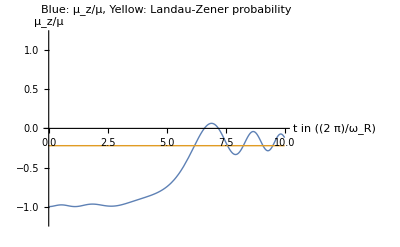

```mathematica
Plot[{2 Abs[h[t]]^2-1/.solLZ,1-2Exp[-π/2 ωR^2/(20ωR bLZ)]/.LZConditions},{t,0,1/bLZ},PlotRange->{-1.2,1.2},PlotStyle->Thick,AxesLabel-> {t"in " [(2π)/Subscript[ω, R]],"μ_z/μ"},PlotLabel->"Blue: μ_z/μ, Yellow: Landau-Zener probability"]
```

```mathematica
(*A NON-LINEAR SWEEP*)
```

```mathematica
ωLZNonlinear[t_]:=ω0+ ωR*(-10+20*(b*t)^2); (*how the frequency is swept*)
```

```mathematica
ϕLZNonlinear[t_]:=Integrate[ωLZNonlinear[tp],{tp,0,t}]
```

```mathematica
LZConditionsNonlinear={ω0->2*Pi*0,ωR->2*Pi*3,ϕ[t]->ϕLZNonlinear[t],b->0.1};
```

```mathematica
LZEqn1NSolveNonlinear=LZEqn1NSolve/.LZConditionsNonlinear;
```

```mathematica
LZEqn1NSolveNonlinear=LZEqn1NSolveNonlinear/.LZConditionsNonlinear;
```

```mathematica
LZEqn2NSolveNonlinear=LZEqn2NSolve/.LZConditionsNonlinear;
```

```mathematica
LZEqn2NSolveNonlinear=LZEqn2NSolveNonlinear/.LZConditionsNonlinear;
```

```mathematica
solLZNonlinear=First@NDSolve[{LZEqn1NSolveNonlinear,LZEqn2NSolveNonlinear,g[0]==1,h[0]==0},{g,h},{t,0,1/0.1},MaxSteps->10000];
```

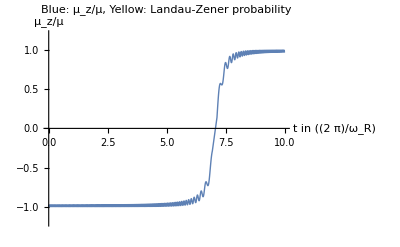

```mathematica
Plot[{2 Abs[h[t]]^2-1/.solLZNonlinear,1-2Exp[-π/2 ωR^2/(20ωR bLZ)]/.LZConditionsNonlinear},{t,0,1/0.1},PlotRange->{-1.2,1.2},PlotStyle->Thick,AxesLabel-> {t"in " [(2π)/Subscript[ω, R]],"μ_z/μ"},PlotLabel->"Blue: μ_z/μ, Yellow: Landau-Zener probability"]
```

```mathematica
(*LZ SWEEP ON A BLOCH SPHERE*)
```

In order to visualize how the quantum state evolves on the Bloch sphere in a Landau-Zener sweep it is easier to solve the classical analog of this problem of a magnetic moment in a rotating magnetic field. The classical system is three coupled differential equations.

{Lx→InterpolatingFunction[…],Ly→InterpolatingFunction[…],Lz→InterpolatingFunction[…]}

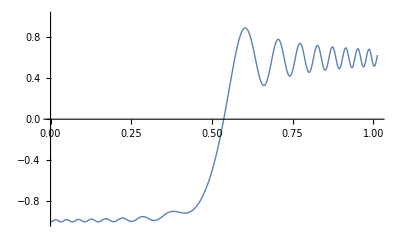

```mathematica
ω0Classical=2π 0;
ωRClassical = 2π 1*Pi ;
bClassical =.1 *Pi^2;
ωoftClassical[t_]:=ω0Classical-10 ωRClassical+20ωRClassical bClassical t
phioftClassical[t_]:=Integrate[ωoftClassical[tp],{tp,0,t}]
sol2Classical=First@NDSolve[{Lx'[t]==Ly[t](ω0Classical-ωoftClassical[t]),Ly'[t]== Lz[t] ωRClassical -Lx[t](ω0Classical-ωoftClassical[t]),Lz'[t]== -Ly[t]ωRClassical,Lz[0]==-1,Ly[0]==0,Lx[0]==0},{Lx,Ly,Lz},{t,0,1/bClassical},MaxSteps->10000]
Plot[Lz[t]/.sol2Classical,{t,0,1/bClassical},PlotRange->{-1,1},PlotStyle->Thick]
```

```mathematica
Show[ParametricPlot3D[{Lx[t],Ly[t],Lz[t]}/.sol2Classical,{t,1/bClassical 0.0,1 1/bClassical},PlotRange->{-1,1},AxesLabel->"μ_z/μ"],Graphics3D[{Opacity[0.2],Sphere [{0,0,0},1]}],AxesLabel->{"μ_x","μ_y","μ_z"},ViewPoint->{0.8,-2,1.5},ViewVertical->{0,0,1}]
```

-Graphics3D-

### Early Atomic Physics

### The Hydrogen Atom

### The Alkalis

### Spin-Orbit Coupling

### Hyperfine Structure

### Interaction of Atoms with Radiations

Two-level system (Rabi problem)

Readily observed in radio-frequency (RF) spectroscopy for e.g . transitions between Zeeman or hf levels . These transitions also have negligible spontaneous emission, so n most cases the atoms evolve coherently .

Population in excited state: non-perturbative solution

```mathematica
P2[t_,δ_,Ω_]:=(Ω^2/(Ω^2+δ^2))*Sin[Sqrt[Ω^2+δ^2]*t/2]^2
```

```mathematica
Manipulate[Plot[P2[t,δ,1],{δ,-3,3},PlotRange->{0,1}],{t,0,6*Pi}]
```

Bloch vector, Bloch sphere, and the Optical Bloch Equations

A pure quantum state ψ = (c1, c2) could be represented by a density matrix ρ. On the other hand, a quantum state on the Bloch sphere is specified by three coordinates (u,v,w). What is the correspondence between (u,v,w) and the density matrix ρ?  One can show that the density matrix corresponding to the state (u,v,w) is given by

Bloch vector

```mathematica
BlochVector[u_,v_,w_]:={u,v,w}
```

Density matrix - Bloch sphere correspondence

```mathematica
ρBloch[u_,v_,w_]:=(IdentityMatrix[2]+u*PauliMatrix[1]+v*PauliMatrix[2]+w*PauliMatrix[3])/2;
```

```mathematica
ρBloch[u,v,w]//MatrixForm
```

((1+w)/2 | 1/2 (u-ⅈ v)
1/2 (u+ⅈ v) | (1-w)/2)

With this, we can show that given a density matrix {{ρ11, ρ12}, {ρ21, ρ22}} where ρ12 = ρ21* then 

u = ρ_12 + ρ_21
v = - ⅈ (ρ_12 - ρ_21)
w = 1 - ρ_22

Evolution of Bloch vector: Optical Bloch equations without damping

The Bloch vector for the ideal two-level system and its evolution is entirely dictated by the Rabi frequency ωR and the detuning δ. Without damping, the evolution of the state vector is given by:

```mathematica
DBlochVectorDt[u_,v_,w_]:={δ*v, -δ*u+ωR*w,-ωR*v}
```

```mathematica
DBlochVectorDt[u,v,w]//MatrixForm
```

(v δ
-u δ+w ωR
-v ωR)

The magnitude of the Bloch vector for a pure state is constant

The Bloch vector is perpendicular to its time derivative. This implies that its magnitude is constantly unity. This means that the Bloch vector corresponds to the position vector of points on the surface of a sphere of unit radius -- the Bloch sphere.

```mathematica
Dot[BlochVector[u,v,w],DBlochVectorDt[u,v,w]]//FullSimplify
```

0

Look at the form of the time derivative of the Bloch vector, it has the form dB/dt = B x W where “x” is the cross product and W is the vector:

```mathematica
W[ωR_,δ_]:={ωR,0,δ}
```

```mathematica
W[ωR,δ]//MatrixForm
```

(ωR
0
δ)

The Bloch vector precesses around the vector W with rate equal to the length of W. The evolution of the BLoch vector is similar to that of a magnetic moment in a magnetic field, where the magnetic moment precesses around the magnetic field.

Bloch sphere

```mathematica
BlochSphere = Graphics3D[{Opacity[0.2],Sphere[],Black,Opacity[1.],
PointSize[.02],Point[{0,0,0}],Point[{1,0,0}],Point[{-1,0,0}],Point[{0,1,0}],Point[{0,-1,0}],Point[{0,0,1}],Point[{0,0,-1}],
Line[{{0,1,0},{0,-1,0}}],
Line[{{0,0,1},{0,0,-1}}],
Line[{{1,0,0},{-1,0,0}}],
Text[Style[Row[{"|0⟩=",MatrixForm[{1,0}]}], 10], {0,0,1.3 }],
Text[Style[Row[{"|1⟩=",MatrixForm[{0,1}]}], 10], {0,0,-1.3 }],
Text[Style[Row[{"|R⟩"}], 10], {0,1.3 ,0}],
Text[Style[Row[{"|L⟩"}], 10],{0,-1.3 ,0}],
Text[Style[Row[{"|+⟩"}], 10], {1.6 ,-0.25,0}],
Text[Style[Row[{"|-⟩"}],10],{-1.5 ,0.3,0}]}];
```

```mathematica
Append[BlochSphere, Boxed->False]
```

-Graphics3D-

Ramsey Fringes

Driven Damped Lorentz Oscillator

Driven damped Lorentz oscillator

Optical Bloch equations with damping

In order to get the damped version of the optical Bloch equations, we simply add damping terms to each of du/dt, dv/dt, and dw/dt. Since u, v are terms related to coherences and w is related to the population in the excited state, the damping factor is -Γ/2 for u, v and -Γ for w.

Optical Bloch Equations with Damping

The Optical Bloch equations with damping are

```mathematica
DBlochVectorDtWithDamping[u_,v_,w_]:={δ*v-(Γ/2)*u, -δ*u+ωR*w-(Γ/2)*v,-ωR*v-Γ*(w-1)};
```

```mathematica
DBlochVectorDtWithDamping[u,v,w]//MatrixForm
```

(-(u Γ)/2+v δ
-(v Γ)/2-u δ+w ωR
-((-1+w) Γ)-v ωR)

Steady-state solution for the Optical Bloch equations

We typically don’t care about the transient solutions to the Optical Bloch equations because the timescales are often not relevant. Rather, the steady-state solution is much more relevant to us:

```mathematica
BlochSteadyState[ωR_,δ_,Γ_]:=(1/(δ^2+ωR^2/2+Γ^2/4))*{ωR*δ, ωR*Γ/2,δ^2+Γ^2/4}
```

Steady-state population of excited state

The steady-state population of the excited state is related to w via w = 1 - 2 ρ_22. So,

```mathematica
ρ22SteadyState[ωR_,δ_,Γ_]:= (1-Dot[BlochSteadyState[ωR,δ,Γ],{0,0,1}])/2//FullSimplify
```

```mathematica
ρ22SteadyState[ωR,δ,Γ]
```

ωR^2/(Γ^2+4 δ^2+2 ωR^2)

Notice that for very strong drive, i.e. the Rabi frequency ωR becomes large relative to the damping and detuning, the excited state population saturates to 1/2:

```mathematica
Limit[ρ22SteadyState[ωR,δ,Γ],{ωR->Infinity}]
```

1/2

The Optical Absorption Cross-section

Consider a sample of N atoms with thickness Δz. Light with intensity I(w,z) along the z-axis with frequency is incident on the sample. The attenuation of the light is modeled by an exponential decay:

dI(ω,z)/dz = - N σ(ω) I(ω,z) = - (N_1- N_2) σ(ω) I(ω,z)

Here N_1are the absorbing atoms and N_2are the emitting atoms (due to stimulated emission). By conservation of energy, the light attenuated per unit volume is the same as the amount of light that the atoms scatter out of the beams due to spontaneous emission. So, we have an equation:

(N_1 - N_2) σ(ω) I(ω) = N_2 ℏω Γ

Now, since we know w = (N_1 - N_2)/N and ρ_22= N_2/N, we can substitute in these quantities into the equation above and solve for the cross section σ(ω):

w(ω,δ,Γ) σ(ω) I(ω) = ρ_22(ω,δ,Γ) ℏω Γ

```mathematica
Solve[Dot[BlochSteadyState[ωR,δ,Γ],{0,0,1}]*σ*Intensity==ρ22SteadyState[ωR,δ,Γ]*ℏ*ω*Γ,σ]//FullSimplify
```

{{σ→(Γ ω ωR^2 ℏ)/(Intensity Γ^2+4 Intensity δ^2)}}

Okay, but notice that the absorption cross-section should not depend on the intensity of the light used. To see this, recall that the intensity of the light field is proportional to only the magnitude of the electric field squared. Moreover, there is a ωR^2 term in the denominator for σ, which is also proportional to the electric field magnitude squared. 

This means that we can cancel the electric field magnitude. After some manipulations, the absorption cross-section is dependent only on ω, ω_0, and Γ and takes the form:

σ(ω) ~ Γ/ω0^2 * Lorentzian(ω, Γ) ~  (1/ω0^2) *  Γ^2 / (δ^2 + Γ^2/4)

where the Lorentzian(ω, Γ) = gH(ω) is the lineshape function (Cauchy distribution). Here, “H” denotes homogeneous. Where does the factor of 1/ω0^2 come from? Notice that in the expansion of the Rabi frequency into the electric field squared multiplied by the matrix element squared, the electric field squared cancels with that which appears in the intensity term. The remains terms are ω and the matrix element squared, which is proportional to Γ. Let us be hand-wavy here and say that ω ~ ω0. Since we know that Γ is proportional to 1/ω0^3, the overall factor ωΓ is roughly 1/ω0^2.

```mathematica
gH[ω_,ω0_,Γ_]:=(1/(2*Pi))*Γ/((ω - ω0)^2 + Γ^2/4);
```

```mathematica
σ[ω_,ω0_,Γ_]:=(3*(Pi^2*c^2)/ω0^2)*Γ*gH[ω,ω0,Γ];
```

```mathematica
σ[ω,ω0,Γ]
```

(3 c^2 π Γ^2)/(2 (Γ^2/4+(ω-ω0)^2) ω0^2)

Note the factor of 3 in the equation above. In a more general case, this factor can take values between 0 and 3, as it is given by g_2/g_1the ratio of the degeneracy levels. For alkali atoms, the D2 transition is s-p, and the ratio is indeed 3.

Resonance absorption cross section

The absorption cross-section peaks on resonance:

```mathematica
σ0=σ[ω0,ω0,Γ]
```

(6 c^2 π)/ω0^2

which is proportional to the square of the wavelength of the transition:

```mathematica
σ0/.{ω0->2Pi*c/λ0}
```

(3 λ0^2)/(2 π)

One thing to note from this is that the cross-section of atoms in photon-atom interaction can be much larger than the size of the atom. One could say that the “collisions” between atoms and photons have a large resonant enhancement.

Saturation Intensity

In order to quantity the amount of saturation, we return to the equation:

(N_1 - N_2) σ(ω) I(ω) = N_2 ℏω Γ

which after calling σ(ω) I(ω)/ℏω Γ = r and assuming N_1+N_2=N=1, we have

(N_1 - N_2) r = N_2  ------> N_2/N_1= r / (r+1) 

Solving for N_2 using N_1+N_2 = N = 1 gives

```mathematica
Solve[N2/(1-N2)==r/(r+1),N2]//FullSimplify
```

{{N2→r/(1+2 r)}}

We define the saturation parameter as 

s = I(ω)/I_sat(ω)=2r=2σ(ω) I(ω)/ℏωΓ  = I(ω) * (2σ(ω)/ℏωΓ)

```mathematica
s[ω_]:=Intensity[ω]*(2σ[ω,ω0,Γ])/(ℏ*ω*Γ)
```

From here, one can define the saturation intensity as a function of the frequency of the driving field:

```mathematica
ISat[ω_,ω0_,Γ_]:=ℏ*ω*Γ/(2*σ[ω,ω0,Γ])
```

The saturation intensity is minimized on resonance. This value is often referred to as the saturation intensity:

```mathematica
ISatMin=ISat[ω0,ω0,Γ]/.{ω0->2*Pi*c/λ0}
```

(2 c π^2 Γ ℏ)/(3 λ0^3)

Alternatively, we could also define the saturation intensity from the steady-state solution of the Bloch equations. Knowing that

N_1-N_2=1/(1+2r)=w

we obtain another definition of the saturation parameter in terms of the Rabi frequency and linewidth of the transition: 

s = 2r=I/I_sat=2Ω^2/Γ^2

```mathematica
s=2*ωR^2/Γ^2
```

(2 ωR^2)/Γ^2

Power Broadening

Suppose we are doing absorption imaging of atoms. What we observe is actually the attenuation of the imaging light due to the atoms. What we measure is proportional to the quantity w*σ(ω), which has the form:

```mathematica
wSS=1/(1+s*Γ^2/(Γ^2+4 (ω-ω0)^2));
```

```mathematica
σPowerBroadening[ω_,ω0_,Γ_,σ0_]:=σ0*Γ^2/(Γ^2+4 (ω-ω0)^2);
```

where in the definition for w in steady state we have used s = I/I_sat with I_sat being the saturation intensity, and rewriting I(ω)/I_sat(ω) as I(ω)/[ I_sat*σ0/σ(ω) ]. With these, we get:

```mathematica
wSS*σPowerBroadening[ω,ω0,Γ,σ0]//FullSimplify
```

(Γ^2 σ0)/((1+s) Γ^2+4 (ω-ω0)^2)

which is a Lorentzian with full-width at half-maximum:

```mathematica
ΔwFWHM=Γ*Sqrt[1+s];
```

We see that the lineshape is broadened as the light intensity approaches and exceeds the saturation intensity I_sat. This is call power broadening.

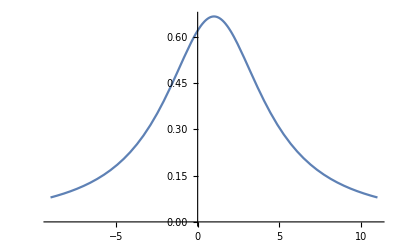

```mathematica
Plot[wSS*σPowerBroadening[ω,1,6,1]/.{s->0.5,Γ->6,ω0->1},{ω,-10+1,10+1}]
```

Doppler Broadening

AC-Stark Effect and Light Shift

In the rotation frame and time-dependent perturbation theory, the Hamiltonian in the presence of an oscillatory driving field is given by

```mathematica
HACStark[δ_,ωR_]:=(1/2)*{{δ,ωR},{ωR,-δ}};
```

```mathematica
HACStark[δ,ωR]//MatrixForm
```

(δ/2 | ωR/2
ωR/2 | -δ/2)

The eigenvalues are:

```mathematica
Eigenvalues[HACStark[δ,ωR]]
```

{-1/2 √(δ^2+ωR^2),1/2 √(δ^2+ωR^2)}

For ωR = 0, the energies are the same as those for the unperturbed system where the levels are spaced by δ. 

Normally, light shifts are important in regimes where the detuning is large (δ  >> ωR). In this case, we can do a Taylor series expansion of the eigenvalues to get the light shifts in the high-detuning regime:

The lower level’s energy is shifted by  - ωR^2 / 4δ

```mathematica
FullSimplify[Series[Eigenvalues[HACStark[δ,ωR]][[1]],{ωR,0,2}],δ>0]
```

-δ/2-ωR^2/(4 δ)+O[ωR]^3

whereas the higher level’s energy is shifted by + ωR^2 / 4δ

```mathematica
FullSimplify[Series[Eigenvalues[HACStark[δ,ωR]][[2]],{ωR,0,2}],δ>0]
```

δ/2+ωR^2/(4 δ)+O[ωR]^3

Notice that the light shift is proportional to the square of the Rabi frequency, so it is proportional to the light intensity. The light shift is also inversely proportional to the detuning. It is also dependent on the sign of the detuning, which is important for optical dipole trapping.

DC Stark Effect

DC Stark Effect for a Diatomic Molecule

Oscillator Strength

```mathematica
(*Check homework in C. J. Foot*)
```

```mathematica
(*Check Martin's notes*)
```

Selection Rules

### Doppler-Free Spectroscopy

### Laser Cooling and Trapping

The Scattering Force

Consider a laser beam with intensity I. The radiation pressure is given by I/c where c is the speed of light. Pressure has units of force over area, so the radiation force is given by F = AI/c. For atoms, the area term is effectively replaced by the absorption cross section σ_0 which is typically much larger than the size of atoms, and as a result radiation force can have a large effect on atoms.

A more precise expression for the scattering force light exerts on an atom is given as follows: force is equal to the rate of change of momentum. Each photon carries momentum ℏk, and so it remains to calculate the rate at which the ℏk quanta impart momentum on the atom. This rate is the scattering rate.

The scattering rate R is given in terms of the rate of spontaneous emission multiplied by “how many atoms there are to scatter” which is the excited state population ρ_22. So, the scattering rate is simply R = Γρ_22. From the steady-solution to the optical Bloch equations, this is

```mathematica
RscatΩ[δ,Γ,Ω]=Γ*(ωR^2/4)/(δ^2+Ω^2/2+Γ^2/4);
```

Here the detuning is could be the detuning from the laser light to the resonance frequency plus the Doppler shift kv where v is the velocity of the atoms. Since the Rabi frequency is often not known, we often express the scattering rate in terms of the saturation parameter s = 2Ω^2/Γ^2. With this,

```mathematica
Rscat[δ,Γ,s]=(Γ/2)*s/(4*δ^2/Γ^2+(1+s));
```

The scattering force is therefore

```mathematica
Fscat = ℏ*k*Rscat[δ,Γ,s]
```

(k s Γ ℏ)/(2 (1+s+(4 δ^2)/Γ^2))

Relying only on the scattering force, one could compute roughly what the stopping distance is roughly. Once the force is known, we can divide by the mass of the atom to obtain a deceleration. Now using 

v0^2 - v^2 = 2az, 

we can could set the final velocity to zero to get z, the stopping distance. For alkali atoms with initial velocities roughly about 360 m/s (speed of sound), the stopping distance is roughly a 1 meter.

This is of course a very rough calculation because of the Doppler effect changes as the atom slows down.

Zeeman Slower

Suppose that we want to decelerate atoms to zero velocity with constant deceleration within some distance L0. Then the velocity of the atoms as a function of the initial velocity and the distance z over the length L0 is

```mathematica
v[v0,z,L0]=v0*Sqrt[1-z/L0];
```

This formula is due to Newtonian kinematics. Now, as the atom slows down, we want to compensate for the changing Doppler effect by changing the resonance frequency of the atoms by changing the Zeeman effect. Suppose the Zeeman shift is for a magnetic field B is given by μ_B B/ℏ then the resonance condition is satisfied whenever 

ω + μ_BB(z)/ℏ = ω_0+k v

Solving for B(z) gives

```mathematica
Solve[ω+μ*B/ℏ==ω0+k*v0*Sqrt[1-z/L0],B]//FullSimplify
```

{{B→((k v0 √(1-z/L0)-ω+ω0) ℏ)/μ}}

Let μ_B B_bias = ℏ(ω - ω_0) and B_0 = ℏ k v_0/μ_B then we have

```mathematica
B[z]=B0*Sqrt[1-z/L0]+Bbias
```

Bbias+B0 √(1-z/L0)

Note that a lot of these calculations are back-of-the-envelope type that might differ from experimental results due to physical effects such as imperfect field, field fringing, etc. However, they provide a good guideline for building a Zeeman slower. 

As an example, we could calculate B0 for Na23 atoms traveling with speed about 1000 m/s.

```mathematica
B0Na23=(6.626*10^(-34)/(590*10^(-9)))*1000/(9.27*10^(-24)) (*Tesla*)
```

0.121149

We need B0 of about 0.12 Teslas.

Optical Molasses

Consider an atom subjected to two counter-propagating beams along the z axis. Suppose the atom is moving with velocity v along the z-axis. The scattering force on the atom due to both beams is given by 

F_scat = F_scat(ω - ω_0-kv) - F_scat(ω -ω_0+kv)

Consider the kv << Γ limit, we can Taylor expand the scattering force terms as 

F_scat = F_scat(ω - ω_0) -  kv (dF_scat/dω)   - F_scat(ω -ω_0+kv) - kv (dF_scat/dω)  = -2kv(dF_scat/dω)

Damping coefficient for low velocities

Notice that this force is velocity-dependent: so it is a damping force. If we write it as F = - αv then the damping coefficient α is simply 

α = 2k * (dF_scat/dω)

since k = ω/c, we can express as

```mathematica
2*(ω/c)*D[Fscat/.{k->ω/c,δ->ω-ω0},ω]
```

(2 ω ((s Γ ℏ)/(2 c (1+s+(4 (ω-ω0)^2)/Γ^2))-(4 s ω (ω-ω0) ℏ)/(c Γ (1+s+(4 (ω-ω0)^2)/Γ^2)^2)))/c

Consider the limit where I/I_sat<<1 and noticing that the second term is much larger than the first term, we simplify this to:

```mathematica
αDamping=4ℏ*k^2*s*(-2δ/Γ)/(1+(2δ/Γ)^2)^2
```

-(8 k^2 s δ ℏ)/(Γ (1+(4 δ^2)/Γ^2)^2)

Why do we have to assume I/I_sat << 1? This is because this simple treatment of optical molasses is only valid for intensities well below the saturation intensity, where the force from each beam acts independently. For real atoms (as opposed to theoretical two-level systems),  the light field needs to be treated as a standing wave.

Force as a function of velocity

Here we plot the net scattering force along z as a function of velocity for various detunings.

```mathematica
FscatCounterProp=(k s Γ ℏ)/(2 (1+s+(4(δ-k*v)^2)/Γ^2))-(k s Γ ℏ)/(2 (1+s+(4 (δ+k*v)^2)/Γ^2))/.{ℏ->1,s->0.1,k->1};
```

```mathematica
Manipulate[Plot[FscatCounterProp/.{δ->x*Γ}/.{Γ->1},{v,-10*Γ,10*Γ}/.{Γ->1},PlotRange->Full],{x,-5,0.5}]
```

The capture velocity is approximately v_c ~ Γ/k

Note that the analysis above is still quite naive since we have not considered the effect of heating due to fluctuations in the force. It is due to the heating caused by fluctuations in the the forces that gives rise to the Doppler cooling limit.

Doppler Cooling Limit

In this subsection we derive the Doppler cooling limit. Consider the forces acting on an atom in the presence of a laser beam. There are two forces, one associated with absorption and one associated with spontaneous emission. 

On average, the force due to absorption is the same as the familiar scattering force. 
On average, the force due to spontaneous emission is zero, since the momentum kick imparted on the atom as it emits a photon is random. 

Now we consider the fluctuations in the two forces. 

Spontaneous emission results in the atom making a random walk in momentum space for each emission. A random walk of N steps gives a mean displacement proportional to Sqrt[N]. Given a scattering rate R_scat, the atom scatters N photons over a time t = N/R_scat. 
The mean square velocity of the atom becomes 

E[v^2] = N * v_r^2 

where E[.] denotes the expectation value and v_r is the recoil velocity, which is given by Mv_r=ℏk. This says that the scattering of N photons increase the mean square velocity to an expected value of N times the recoil velocity squared. Now consider only along the z-axis, there is a geometric factor that the average of cos^2(θ) which is 1/3 for isotropic spontaneous emission:

E[v_z^2] = η * R_scat *  t  * v_r^2 

 The fluctuations in the scattering force is due to the fact that the atom does not always absorb the same number of photons in a duration of t. Assuming that the absorption events follow Poisson statistics, the mean square velocity along the propagation direction of the beams also increases as 
 
 E[v^2] = R_scat*t  * v_r^2
 
Even though the scattering forces from the propagating light beams tend to cancel, the fluctuations due to the beams are cumulative. The atoms have equal probability of absorbing a photon from the right or left beam, so it is equally likely to get a random kick to the right or to the left, leading to a random walk of velocity along the beams.  

The Doppler limit is derived from calculating the equilibrium state between heating and cooling. To this end, we look at how the kinetic energy along the z-axis changes as a function of time without heating (so there is only cooling due to the scattering forces):

d/dt (M E[v_z^2]/2) = Mv_z* dv_z/dt = v_z* (- α_damping * v_z) =  - α_damping*v_z^2

By adding the equations for x- and y-directions, we obtain the rate of change of the kinetic energy of the atom:

dE/dt =  - 2 α_damppingE/M =  - E/τ_damping

We see that the kinetic energy decreases exponentially in time without heating. Now including the effect of heating, we find 

1/2 * M * (d/dt) E[v_z^2] =  - α E[v_z^2] + (1+η)  * 2 E_r*R_scat

where once again E[.] denotes expectation values and E_r = Mv_r^2/2  is the recoil energy.  

In steady state, the time derivative is zero. Moreover, for the typical configuration with 6 laser beams in 3 dimensions, the term 1 + η is actually 1 + 3η, where η = 1/3 (assuming isotropic spontaneous emission), so the term 

1+η becomes 1 + 3η  = 2 in 3D.

Settings the LHS to zero we find that in steady state:

E[v_z^2] = (2 E_r) * (2R_scat/α) 

By means of the equipartition theorem: M<v_z^2>/2 = k_BT/2, we can now derive the expression for the steady state temperature:

```mathematica
Solve[kB*T/2 == (M/2)*2*Er*2Rsc/α/.{Er->(ℏ*k/M)^2*M/2, Rsc->(s Γ)/(2 (1+s+(4 δ^2)/Γ^2)),α->-(8 k^2 s δ ℏ)/(Γ (1+(4 δ^2)/Γ^2)^2)},T]//FullSimplify
```

{{T→-((Γ^2+4 δ^2)^2 ℏ)/(8 kB δ ((1+s) Γ^2+4 δ^2))}}

In the low saturation regime, we may simplify this as

```mathematica
TDoppler[δ]=-((Γ^2+4 δ^2)^2 ℏ)/(8 kB δ ((1+s) Γ^2+4 δ^2))/.{s->0}
```

-((Γ^2+4 δ^2) ℏ)/(8 kB δ)

```mathematica
δDopplerMin=Solve[D[TDoppler[δ],δ]==0,δ][[1]]
```

{δ→-Γ/2}

```mathematica
TDopplerLimit = TDoppler[δ]/.δDopplerMin
```

(Γ ℏ)/(2 kB)

We have just derived the expression for the Doppler cooling temperature limit. 

As a quick tip to remember, by dimensional analysis and the nature of the scattering force, we can get to k_B T = ℏ Γ  easily. However, there is an also extra factor of 1/2 on the Γ.

Magneto-Optical Trap

We will skip over the principle of operation of the MOT (as one should already know this by now) and will focus only on the quantitative analysis of the cooling and trapping forces in the MOT. 

The MOT combines the optical molasses technique with a quadrupole magnetic field which causes a spatially varying force (imbalance in the scattering forces) which traps the atoms. In almost all cases, the magnetic field inside the MOT is zero at the center of the trap and its magnitude increases linearly in every direction  for small displacements from the center. Due to Maxwell’s equations, div B = 0, which implies 

dB_x/dx = dB_y/dy = (-1/2) dB_z/dz.

The light used in the MOT is three pairs of counter propagating, circularly polarized light. The counter propagating beams in each direction have opposite handedness. The handedness of each beam is dependent on the configuration of the magnetic field (which affects how the Zeeman levels shift along a certain direction).

Let us focus on the z-direction. The Zeeman shift in frequency is proportional to z: β*z where 

β = (g * μ_B/ℏ) * dB_z/dz.

The net scattering force due to the beams and magnetic field gradient is the same as before, with ω0 modified by the Zeeman shift:

F_MOT =  - 2 * (dF_scat/dω) * (kv + β z) =  - α_damp * v - (α_damp/k) * β * z

We see that the force has two terms. The (velocity-dependent) damping term, which comes from the optical molass, is responsible for cooling. The spatially-dependent term, which comes from the magnetic field gradient, is responsible for trapping. The spring constant for the restoring force (second term) is α_damp * β/k.

Why can we see the MOT with our naked eye?

At equilibrium the MOT absorbs and emits the same amount of light. This means that a large cloud of atoms in a MOT scatters a significant amount of light and can therefore be seen with the naked eye (of course the wavelength of the scattered light has to be in the visible range).

### Optical Trapping

Dipole Force

Optical Dipole Trap

The Gaussian Beam

Sisyphus Cooling (Polarization Gradient Cooling)

Raman Cooling

### Magnetic Trapping

### Evaporative Cooling

### Statistical Mechanics

### Bose-Einstein Condensation

### Degenerate Fermi Gas

### Feshbach Resonance

### Quantitative Analysis of Density Distributions

Trapped Atomic Gases

Fitting Functions for trapped and expanded Fermi gases

Absorption Imaging

Polarization Rotation Imaging

The Inverse Abel Transformation

### Miscellaneous Calculations

Imbalance

```mathematica
Imbalance[TopB_, TopA_]:=(TopB-TopA)/(TopB+TopA);
```

```mathematica
N[Imbalance[485,365]]
```

0.141176

Minimum saturation intensities for D2 lines of Na23 and Li6

```mathematica
ISatMin[Γ_,λ0_]:=(2 c π^2 Γ ℏ)/(3 λ0^3);
```

```mathematica
ISatMin[ΓLi6D2,λLi6D2]/.{c->cSOL,ℏ->hbar} (*Li6 D2 in W/m^2*)
```

25.4084

```mathematica
ISatMin[ΓNa23D2,λNa23D2]/.{c->cSOL,ℏ->hbar} (*Na23 D2 in W/m^2*)
```

62.6002

A weird Landau-Zener sweep

```mathematica
HLZWeird = (ℏ/2)*{{ω0,ωR*(E^(-I*ϕ[t])+E^(-I*(ϕ[t]+δ)))},
{ωR*(E^(+I*ϕ[t])+E^(I*(ϕ[t]+δ))),-ω0}};
```

```mathematica
HLZWeird//MatrixForm
```

((ω0 ℏ)/2 | 1/2 (ⅇ^(-ⅈ ϕ[t])+ⅇ^(-ⅈ (δ+ϕ[t]))) ωR ℏ
1/2 (ⅇ^(ⅈ ϕ[t])+ⅇ^(ⅈ (δ+ϕ[t]))) ωR ℏ | -(ω0 ℏ)/2)

The coupled equations for g(t) and h(t) are then:

```mathematica
LZEqn1Weird=g'[t]==-I(ω0/2*g[t]+1/2 (ⅇ^(-ⅈ ϕ[t])+ⅇ^(-ⅈ (δ+ϕ[t]))) ωR*h[t]);
```

```mathematica
LZEqn2Weird=h'[t]==-I(1/2 (ⅇ^(ⅈ ϕ[t])+ⅇ^(ⅈ (δ+ϕ[t]))) ωR*g[t]-ω0/2*h[t]);
```

Let us set ω0 = 0 because it does not contribute to the dynamics of the problem. Let us also set ωR = 2π. Consider the a linear sweep ϕ(t) defined as:

```mathematica
ωLZWeird[t_]:=ω0+ ωR*(-10+20*b*t); (*how the frequency is swept*)
```

```mathematica
ϕLZWeird[t_]:=Integrate[ωLZWeird[tp],{tp,0,t}]
```

Now we solve: Instead of changing the sweep rate, one can change the Rabi frequency instead

```mathematica
LZConditionsWeird={ω0->2*Pi*0,ωR->2*Pi*0.1,ϕ[t]->ϕLZWeird[t],b->0.1,δ->0.1};
```

```mathematica
LZEqn1Weird=LZEqn1Weird/.LZConditionsWeird;
```

```mathematica
LZEqn2Weird=LZEqn2Weird/.LZConditionsWeird;
```

```mathematica
LZEqn1Weird
```

g'[t]==(0.-0.314159 ⅈ) (ⅇ^(-ⅈ (-6.28319 t+0.628319 t^2))+ⅇ^(-ⅈ (1-6.28319 t+0.628319 t^2))) h[t]

```mathematica
solLZWeird=First@NDSolve[{LZEqn1Weird,LZEqn2Weird,g[0]==1,h[0]==0},{g,h},{t,0,1/0.1},MaxSteps->10000];
```

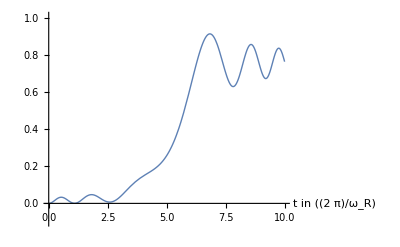

```mathematica
Plot[{Abs[h[t]]^2/.solLZWeird},{t,0,1/0.1},PlotRange->{-0.1,1.01},PlotStyle->Thick,AxesLabel-> {t"in " [(2π)/Subscript[ω, R]]}]
```